Autor: Krzysztof Dragon

# Metody numeryczne w technice

## (kierunek informatyka)

## Projekt 3

Metoda Adamsa-Moultona

Napisać procedurę realizującą algorytm czterokrokowej metody Adamsa-Moultona (argumenty:  f, x_0, y_0, b, n, m).
Wykorzystać metodę iteracji prostej  (m powtórzeń), a jako metodę startową zastosować metodę Rungego-Kutty rzędy czwartego. Zminimalizować liczbę obliczeń funkcji   f.


Korzystając z napisanej procedury wyznaczyć rozwiązanie przybliżone zagadnienia początkowego:

{y'(x)=sin y(x),  x∈[0,25],
y(0)=1.

Obliczenia wykonać dla 10 i 20 kroków.

Na wspólnym rysunku wykreślić rozwiązanie dokładne oraz uzyskane rozwiązania przybliżone.
Wykreślić także, na jednym rysunku, błędy uzyskanych rozwiązań przybliżonych.
Policzyć ponadto błędy maksymalne oraz średnie dla obu siatek.

## Rozwiązanie

```mathematica
(* Metoda Rungiego - Kutty rzędu czwartego *)
metodaRK4[f_,x0_,y0_,h_,n_] :=Module[{xw,yw,k1,k2,k3,,k4,wynik},
xw = Table[x0+i*h,{i,0,n}];
yw = Table[0,{i,0,n}];
yw[[1]] = y0;
Do[
k1=f[xw[[i]],yw[[i]]];
k2 = f[xw[[i]]+h/2,yw[[i]]+h*k1/2];
k3 = f[xw[[i]] + h/2,yw[[i]]+ h*k2/2];
k4 = f[xw[[i+1]],yw[[i]]+ h*k3];
yw[[i+1]] = yw[[i]] + h/6*(k1+2k2+2k3 + k4),
{i,1,n}];
wynik = Transpose[{xw,yw}];
Return[wynik]
]
```

```mathematica
(* Metoda Adamsa-Moultona - czterokrokowa*)
metodaAM[f_,x0_,y0_,b_,n_,nmip_]:= Module[{h,η,xw,yw,m0,m1,m2,m3,m4,b41,b42,b43,b44,b40,wp,wynik},
h = (b-x0)/n;

xw = Table[x0+i*h,{i,0,n}];
yw = Table[0,{i,0,n}];

yw[[1]] = y0;

b40 = 251/720;
b41 = 646/720;
b42 = -264/720;
b43 = 106/720;
b44 = -19/720;

wp = metodaRK4[f,x0,y0,h,3];

Do[yw[[i]] = wp[[i,2]],{i,2,4}];

m1 = f[xw[[4]], yw[[4]]];
m2 = f[xw[[3]], yw[[3]]];
m3 = f[xw[[2]], yw[[2]]];
m4 = f[xw[[1]], yw[[1]]];

η = yw[[4]];

Do[
Do[
m0 = f[xw[[i+1]], η];
η = yw[[i]] + h * (b40*m0+b41*m1+b42*m2+b43*m3+b44*m4),
{j,1,nmip}];

yw[[i+1]] = η;
m4 = m3;
m3 = m2;
m2 = m1;
m1 = f[xw[[i+1]], yw[[i+1]]],
{i, 4, n}];

wynik  = Transpose[{xw,yw}];

Return[wynik];

];
```

```mathematica
(* Dane do projektu *)
```

```mathematica
f[x_,y_] := Sin[y];
x0 = 0.;
y0 = 1.;
b = 25;
n10 = 10;
n20 = 20;
```

```mathematica
(* n = 10*)
wynik10 = metodaAM[f,x0,y0,b,n10,3]
```

{{0.,1.},{2.5,2.80273},{5.,2.95551},{7.5,3.02736},{10.,3.25099},{12.5,2.90026},{15.,3.64529},{17.5,2.3083},{20.,4.03174},{22.5,2.20771},{25.,4.16512}}

```mathematica
(* n = 20*)
wynik20 = metodaAM[f,x0,y0,b,n20,3]
```

{{0.,1.},{1.25,2.16996},{2.5,2.82782},{3.75,3.04463},{5.,3.14535},{6.25,3.12977},{7.5,3.15071},{8.75,3.13299},{10.,3.14798},{11.25,3.13594},{12.5,3.14621},{13.75,3.13774},{15.,3.1448},{16.25,3.13892},{17.5,3.14382},{18.75,3.13974},{20.,3.14314},{21.25,3.14031},{22.5,3.14266},{23.75,3.1407},{25.,3.14233}}

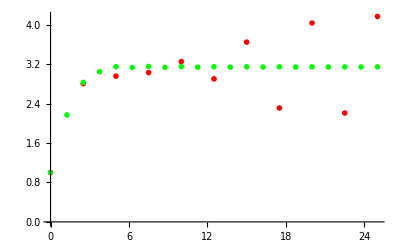

```mathematica
plt10 = ListPlot[wynik10, PlotStyle->{Red, PointSize[0.01]}, PlotRange -> All];
plt20 = ListPlot[wynik20, PlotStyle->{Green, PointSize[0.01]}, PlotRange -> All];
Show[plt10,plt20]
```

```mathematica
(* Rozwiązanie dokładne oraz wspólny wykres*)
```

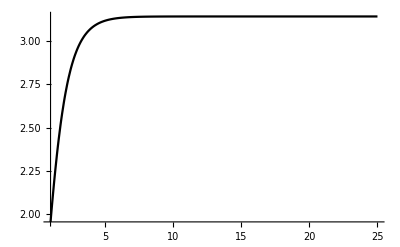

```mathematica
roz = DSolve[{y' [x]==  Sin[y[x]],y[0] == 1}, y[x],x];
pdok = Plot[roz[[1,1,2]], {x,1,25}, PlotRange -> All, PlotStyle->{Black, PointSize[0.008]}]
```

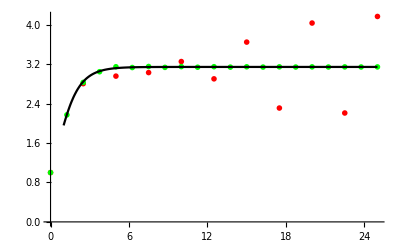

```mathematica
Show[plt10,plt20,pdok]
```

```mathematica
(* Wartości błędów dla n 10 *)
ydok = Table[roz[[1,1,2]] /. {x->wynik10[[i,1]]},{i,1,Length[wynik10]}];
bledy10 = Table [{wynik10[[i,1]], Abs[wynik10[[i,2]] - ydok[[i]]]},{i,1,Length[wynik10]}]
```

{{0.,0.},{2.5,0.0405818},{5.,0.161417},{7.5,0.112211},{10.,0.109566},{12.5,0.24132},{15.,0.503694},{17.5,0.833293},{20.,0.890148},{22.5,0.933885},{25.,1.02353}}

```mathematica
(* Wartości dokładne dla błędów n = 20 *)
ydok = Table[roz[[1,1,2]] /. {x->wynik20[[i,1]]},{i,1,Length[wynik20]}];
bledy20 = Table [{wynik20[[i,1]], Abs[wynik20[[i,2]] - ydok[[i]]]},{i,1,Length[wynik20]}]
```

{{0.,0.},{1.25,0.00561584},{2.5,0.0154967},{3.75,0.010919},{5.,0.0284236},{6.25,0.00475771},{7.5,0.011143},{8.75,0.00802666},{10.,0.00655312},{11.25,0.00560053},{12.5,0.00462743},{13.75,0.00385338},{15.,0.00321123},{16.25,0.00267353},{17.5,0.00222602},{18.75,0.0018538},{20.,0.00154361},{21.25,0.00128538},{22.5,0.00107034},{23.75,0.000891279},{25.,0.000742172}}

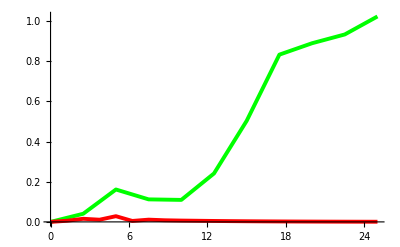

```mathematica
(* Wykres błędów *)
wb10 = ListPlot[bledy10, Joined->True, PlotStyle->{Green, Thickness -> 0.007}];
wb20 = ListPlot[bledy20, Joined->True, PlotStyle->{Red, Thickness -> 0.007}];
Show[wb10,wb20]
```

```mathematica
(* Błąd maksymalny dla n = 10 *)
Max[Transpose[bledy10][[2]]]
```

1.02353

```mathematica
(* Błąd maksymalny dla n = 20 *)
Max[Transpose[bledy20][[2]]]
```

0.0284236

```mathematica
(* Średnia błędów dla n = 10 *)
Mean[Transpose[bledy10][[2]]]
```

0.440877

```mathematica
(* Średnia błędów dla n = 10 *)
Mean[Transpose[bledy20][[2]]]
```

0.00573878